## Utils

```mathematica
SetDirectory["C:\\Users\\drezn\\Dropbox\\Mathematica"];
```

```mathematica
toDeg[r_]:=180.*r/π;
toRad[d_]:=π*d/180.;
negl[v_]:=Abs[v]<10^-9;
magn2[v_]:=v.v;
magn[v_]:=Sqrt[magn2[v]];
flipY[{x_,y_}]:={x,-y};
flipX[{x_,y_}]:={-x,y};
perp[{x_,y_}]:={-y,x};
perpNeg[{x_,y_}]:={y,-x};
refl[v_,n_]:=2(v.n)n/magn2[n]-v;
norm[v_]:=v/magn[v];
clamp[v_,max_:100]:=If[v>max,max,If[v<-max,-max,v]];
ray[p0_,phat_,d_]:=p0+phat*d;
Clear@rot;
rot[p_,st_,ct_]:=Module[{m},
m={{ct,-st},{st,ct}};
m.p];
rot[p_,t_]:=rot[p,Sin@t,Cos@t];
getEquilateral[th_]:=Module[{s=Sin[2π/3.],c=Cos[2π/3.]},
NestList[rot[#,s,c]&,rot[{1.,0.},Sin@th,Cos@th],2]];
(*x0+nx*t=0= >t=-x0/nx;*)
interY[p0_,phat_]:=Module[{t},
t=-p0[[1]]/phat[[1]];
ray[p0,phat,t]];
(*y0+ny*t=0= >t=-y0/ny;*)
interX[p0_,phat_]:=Module[{t},
t=-p0[[2]]/phat[[2]];
ray[p0,phat,t]];
```

-s (dl.dl)+(p-l1)dl==0⇒ s=(p-l1).dl/dl^2

```mathematica
closestPerp[p_,l1_,l2_]:=Module[{dl=l2-l1,s},
s=((p-l1).dl)/(dl.dl);
ray[l1,dl,s]];
```

```mathematica
closestDist[p_,l1_,l2_]:=magn[p-closestPerp[p,l1,l2]]
```

```mathematica
Clear@quadRoots;
quadRoots[a_,b_,c_]:=Module[{det=b^2-4a c,sqrtDet},
If[det<0,Print["quadRoots fail: {a,b,c}="<>ToString@{a,b,c}];False,
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)]];
Clear@interRays;
interRays[p1_,n1_,p2_,n2_]:=Module[{m,b,sols},
m=Transpose[{n1,n2}];(*{{nx1,-nx2},{ny1,-ny2}};*)
If[negl[Det[m]],p1,
b=p2-p1;(*{x2-x1,y2-y1}];*)
sols=LinearSolve[m,b];
ray[p1,n1,sols[[1]]]]
];
```

```mathematica
Second[l_]:=l[[2]];
Third[l_]:=l[[3]];
Fourth[l_]:=l[[4]];
Fifth[l_]:=l[[5]];
```

#### Triangles

```mathematica
cosHalfAngle[cosAngle_]:=Sqrt[(1.+cosAngle)/2];(* careful: plus or minus *)
sinHalfAngle[cosAngle_]:=Sqrt[(1.-cosAngle)/2];(* careful: plus or minus *)
cosDoubleAngle[cosAngle_]:=2*cosAngle*cosAngle-1.; (* cA^2-sA^2 = 2 cA^2-1 *)
sinDoubleAngle[sinAngle_]:=2*sinAngle*Sqrt[1.-sinAngle^2];(* 2 sA cA *)
(* gives cos(A) *)
lawOfCosines[a_,b_,c_]:=(b^2+c^2-a^2)/(2.b c);
getSin[theCos_]:=Sqrt[1.-theCos^2];
sinCosTripleAngle[s_,c_,s2_,c2_]:=Module[{s3,c3},
c3=c2 c-s2 s;
s3=s2 c+s c2;
{s3,c3}];
getSinCosApB[sa_,sb_,ca_,cb_]:={sa cb + sb ca ,ca cb - sa sb};
getSinCosAmB[sa_,sb_,ca_,cb_]:= {sa cb - sb ca,ca cb + sa sb};
getSinApmB[sa_,sb_,ca_,cb_]:= {sa cb + sb ca,sa cb - sb ca};
```

```mathematica
Clear@getTriBisectors;
getTriBisectors[p1_,p2_,p3_]:=Module[{u12,u23,u31},
u12=norm[p2-p1];
u23=norm[p3-p2];
u31=norm[p1-p3];
{
norm[u12-u31],
norm[u23-u12],
norm[u31-u23]
}
];
```

#### Ellipse

```mathematica
ellEqn[a_,x_,y_]:=(x/a)^2+y^2-1;
ellGrad[a_,x_,y_]:=-{x,y a^2};(* (x/a)^2+y^2==1 *)
ellY[a_,x_]:=Sqrt[1-(x/a)^2];
ellError[a_,b_,{x_,y_}]:=(x/a)^2+(y/b)^2-1;
Clear@eccentricity;eccentricity[a_,b_]:=Sqrt[1-(b/a)^2];
focalDistance[a_,b_]:=Sqrt[a^2-b^2];
```

```mathematica
ellRayCoeffs=Module[{r,eqn,sols},
r=ray[{x,y},{nx,ny},s];
eqn=FullSimplify[ellEqn[a,r[[1]],r[[2]]],Assumptions->a>0&&Abs[x]<=a&&(nx^2+ny^2==1)];
FullSimplify[a^2 CoefficientList[eqn,s],a>0]]
```

{x^2+a^2 (-1+y^2),2 (nx x+a^2 ny y),nx^2+a^2 ny^2}

```mathematica
Clear@ellInterRay;
ellInterRay[a_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=nx^2+a^2 ny^2;
c1=2 (nx x+a^2 ny y);
c0=x^2+a^2 (-1+y^2);
ss=quadRoots[c2,c1,c0];
If[ListQ[ss],
ray[{x,y},{nx,ny},#]&/@ss,
{{x,y},{x,y}}]
];
```

Used for Proofs

```mathematica
quadRootsUnprot[a_,b_,c_]:=Module[{det=b^2-4a c,sqrtDet},
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)];
Clear@ellInterRayUnprot;
ellInterRayUnprot[a_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=nx^2+a^2 ny^2;
c1=2 (nx x+a^2 ny y);
c0=x^2+a^2 (-1+y^2);
ss=quadRootsUnprot[c2,c1,c0];
ray[{x,y},{nx,ny},#]&/@ss
];
```

```mathematica
getInterRefl[a_,pfrom_,pto_]:=Module[{norm,theRefl,pnext},
norm=ellGrad[a,pto[[1]],pto[[2]]];
theRefl=refl[pfrom-pto,norm];
pnext=ellInterRayUnprot[a,pto,theRefl][[2]];
pnext];
```

```mathematica
Clear@triSides;triSides[vs_]:=MapThread[(#1-#2)&,{vs,RotateLeft@vs}];
Clear@triLengths;triLengths[vs_]:=magn/@triSides[vs];
triPer[tri_]:=Total[triLengths@tri];
(* a,b,c are side lengths *)
Clear@triAreaHeron;triAreaHeron[{a_,b_,c_}]:=Module[{s},
s=(a+b+c)/2;(* semi perimeter *)
Sqrt[s*(s-a)*(s-b)*(s-c)]];
(* order by oposition to vertices *)
getMedians[t1_,t2_,t3_]:={t2+t3,t1+t3,t1+t2}/2;
getMediansV[vs_]:=.5(vs+RotateLeft@vs);
```

#### Centroids

```mathematica
PerimeterCentroid[vtx_]:=Module[{sides,meds,per,perCentroid},
sides=triLengths@vtx;
meds=getMediansV@@vtx;
per=Total@sides;
perCentroid=Sum[meds[[i]]*sides[[i]],{i,Length@vtx}]/per;
perCentroid];
```

```mathematica
(* vtx mean, perimeter, area *)
getCentroids[vtx_]:={Mean@vtx,PerimeterCentroid@vtx,RegionCentroid[Polygon@vtx]};
```

```mathematica
Clear@getPolyCosines;
getPolyCosines[poly_]:=Module[{us},
us=MapThread[norm[#1-#2]&,{poly,RotateLeft@poly}];
MapThread[(-#1.#2)&,{us,RotateRight@us}]];
```

```mathematica
Clear@polySides;
polySides[poly_]:=MapThread[magn[#1-#2]&,{poly,RotateLeft@poly}];
```

```mathematica
getCircularity[locus_]:=Module[{rads,mean,sd},
rads=magn/@locus;
mean=Mean@rads;
sd=StandardDeviation@rads;
{
"min"->Min@rads,
"max"->Max@rads,
"mean"->mean,
"sd"->sd,
"zscore"->sd/mean
}];
```

```mathematica
(* by zscore *)
getMinCircularity[loci_]:=Module[{l,imin},
l=Select["zscore"/.Quiet@(getCircularity/@loci),NumberQ];
imin=First@First@Position[l,Min[l]];
{l[[imin]],centerNames[[imin]]}]
```

#### Formatting

```mathematica
nfn[v_,n_]:=ToString@NumberForm[v,{n+2,n}];
nfne[v_,n_]:=ToString@NumberForm[v,{n+2,n},NumberFormat->(Row[{#1,If[#3≠"","*10^",""],#3}]&)];
nf[v_]:=ToString@NumberForm[v,{3,2}];
nf1[v_]:=ToString@NumberForm[v,{3,1}];
nf0[v_]:=ToString@IntegerPart[v];
Clear@padn;padn[n_,pads_:3]:=ToString@NumberForm[n,{pads,0},NumberPadding->{"0",""},NumberPoint->""]
```

## Ellipse Invariants

#### Constant Perimeter (Darboux, 1917)

#### -Graphics- Jean-Gaston Darboux (1842-1917)

```mathematica
deltaA[a_]:=Sqrt[a^4-a^2 +1];
```

```mathematica
Clear[darbouxP];
darbouxP[a_,b_:1]:=Module[{a2,b2,delta,per},
a2=a^2;
b2=b^2;
delta=Sqrt[a2^2-a2 b2+b2^2];
per=2Sqrt[2delta-a2-b2](a2+b2+delta)/(a2-b2);
per
];
```

#### Exit angle at x_1 which creates triangular orbit (Garcia, 2019)

-Graphics-

```mathematica
Clear@cosAlpha;cosAlpha[a_,x_]:=Module[{x2,a2,a4,c2,denom},
x2=x^2;
a2=a^2;
a4=a2^2;
c2=a2-1;
denom=c2 Sqrt[a4-c2 x2];
a2 Sqrt[-a2-1+2Sqrt[a4-c2]]/denom];
```

```mathematica
cosAlphaQuad[a_,x1_]:=a^2/Sqrt[a^6+a^4-a^4*x1^2+x1^2]
```

#### Can I find an expression for the next orbit point P_2 in terms of “a” and x_1

```mathematica
Clear@getP2;getP2[a_,x1_]:=Module[{y,p1,norm,ca,sa,p2,normRot,normRotNeg,p2Neg},
y=-ellY[a,x1];
p1={x1,y};
ca=cosAlpha[a,x1]/.{Sqrt[1-a^2+a^4]->d}/.{-1-a^2+2 d->d2};(* to simplify *)
sa=Sqrt[1-ca^2];
norm=ellGrad[a,x1,y];
normRot=rot[norm,sa,ca];
normRotNeg=rot[norm,-sa,ca];
p2=ellInterRayUnprot[a,p1,normRot][[2]]; (* get 2nd solution *)
p2Neg=ellInterRayUnprot[a,p1,normRotNeg][[2]]; 
{p2,p2Neg}];
```

## Triangular Orbits

```mathematica
Clear@getReflData;getReflData [a_,p0_,normal_,sinAlpha_,cosAlpha_]:=Module[{nRot,inter,interNorm,interRefl,nextInter,nextInterNorm},
nRot=rot[normal,sinAlpha,cosAlpha];
inter=ellInterRay[a,p0,nRot][[2]];
interNorm=norm[ellGrad[a,inter[[1]],inter[[2]]]];
interRefl=refl[norm[p0-inter],interNorm];
nextInter=ellInterRay[a,inter,interRefl][[2]];
nextInterNorm=norm[ellGrad[a,nextInter[[1]],nextInter[[2]]]];
{ (* returns an "object" *)
"nRot"->nRot,
"inter"->inter,
"interNorm"->interNorm,
"interRefl"->interRefl,
"nextInter"->nextInter,
"nextInterNorm"->nextInterNorm
}];
```

```mathematica
Options[getOrbitData]={posY->False};Clear@getOrbitData;getOrbitData[a_,x_,OptionsPattern[]]:=Module[{y,o1,n1,ca,sa,sa2,ca2,halfAlpha,pos,neg},
y=-ellY[a,x];
If[OptionValue@posY,y=-y];
o1={x,y};
n1=norm[ellGrad[a,x,y]];
ca=cosAlpha[a,x];
sa=Sqrt[1-ca^2];
pos=getReflData[a,o1,n1,sa,ca];
neg=getReflData[a,o1,n1,-sa,ca];(* orbit at -α *)
(* half-angle to display α at bisector *)
sa2=Sqrt[(1-ca)/2];
ca2=Sqrt[(1+ca)/2];
halfAlpha=rot[n1,sa2,ca2];
{
"ca"->ca,
"sa"->sa,
"halfAlpha"->halfAlpha,
"nRot"->("nRot"/.pos),
"interRefl"->("interRefl"/.pos),
"orbit"->{o1,"inter"/.pos,"nextInter"/.pos},
"normals"->{n1,"interNorm"/.pos,"nextInterNorm"/.pos},
"nRotNeg"->("nRot"/.neg),
"interReflNeg"->("interRefl"/.neg),
"orbitNeg"->{o1,"inter"/.neg,"nextInter"/.neg},
"normalsNeg"->{n1,"interNorm"/.neg,"nextInterNorm"/.neg}
}
];
```

```mathematica
getOrbitData[2.,1.,posY->False]//ColumnForm
```

ca→0.549885
sa→0.835241
halfAlpha→{-0.699945,0.714197}
nRot→{-0.954984,0.296658}
interRefl→{0.999046,0.0436602}
orbit→{{1.,-0.866025},{-1.99582,0.0646022},{1.94314,0.236743}}
normals→{{-0.27735,0.960769},{0.991722,-0.128403},{-0.898933,-0.438085}}
nRotNeg→{0.649963,0.759966}
interReflNeg→{-0.999046,-0.0436602}
orbitNeg→{{1.,-0.866025},{1.94314,0.236743},{-1.99582,0.0646022}}
normalsNeg→{{-0.27735,0.960769},{-0.898933,-0.438085},{0.991722,-0.128403}}

```mathematica
Clear@orbitNormals;orbitNormals[a_,t_]:=Module[{ellP,orbitData},
ellP={N@a * Cos[N@t],Sin[N@t]};
orbitData=getOrbitData[N[a],ellP[[1]],posY->(ellP[[2]]>0)];
{"orbit"/.orbitData,"normals"/.orbitData}
];
```

```mathematica
getAlpha[a_,t_]:=Module[{x1,ca},
x1=a * Cos[t];
ca=cosAlpha[a,a Cos[t]];
ArcCos[ca]];
```

```mathematica
getOrbitCosines[a_,t_]:=Module[{orbit,normals},
{orbit,normals}=orbitNormals[a,t];
getPolyCosines[orbit]];
```

## Major Triangular Centers (Notables)

#### Linha de Euler: bari, ortho, circum, 9-pc all lie on a line (but not incenter)

-Graphics-

```mathematica
getAltBases[p1_,p2_,p3_]:=Module[{sides},
sides={{p2,p3},{p3,p1},{p1,p2}};
MapThread[closestPerp[#1,#2[[1]],#2[[2]]]&,{{p1,p2,p3},sides}]];
```

```mathematica
getIncenter[p1_,n1_,p2_,n2_]:=interRays[p1,n1,p2,n2];
Clear@getBaricenter;getBaricenter[p1_,p2_,p3_]:=Module[{medians},(*(p1+p2+p3)/3;*)
medians=getMedians[p1,p2,p3];
interRays[p1,medians[[1]](*23*)-p1,p2,medians[[2]](*31*)-p2]
];
getOrthocenter[p1_,p2_,p3_]:=Module[{altBases},
altBases=getAltBases[p1,p2,p3];
interRays[p1,altBases[[1]]-p1,p2,altBases[[2]]-p2]
];
getCircumcenter[p1_,p2_,p3_]:=Module[{medians,medianPerps},
medians=getMedians[p1,p2,p3];
medianPerps={
medians[[1]]+norm[perp[p2-p3]],
medians[[2]]+norm[perp[p3-p1]],
medians[[3]]+norm[perp[p1-p2]]
};
interRays[medians[[1]](*2+3*),perp[p2-p3],medians[[2]](*3+1*),perp[p1-p3]]
];
```

#### Nine Point Circle: its center is the circumcenter of the medians, and is tangent to incircle (at Feuerbach point) and all 3 excircles

-Graphics--Graphics-

```mathematica
getNinepointcenter[p1_,p2_,p3_]:=Module[{medians},
medians=getMedians[p1,p2,p3];
getCircumcenter@@medians
];
```

```mathematica
(* shoot ray from incenter *)
getFeuerbachpoint[npc_,incenter_,inradius_]:=Module[{inter},
ray[incenter,norm[incenter-npc],inradius]
];
```

```mathematica
getExcenters[orbit_,normals_]:=Module[{perps,perpsNeg,exc},
perps=perp/@normals;
perpsNeg=perpNeg/@normals;
exc=MapThread[interRays[#1,#2,#3,#4]&,{orbit,perps,RotateLeft@orbit,RotateLeft@perpsNeg}];
exc];
```

#### Gergonne Point: perspector of ABC and its contact triangle Ta, Tb, Tc

## Trilinears

Trilinears x : y : z convert via triangle vertices A, B, C  and sides a, b, c :

```mathematica
Clear@trilinearToCartesian;
trilinearToCartesian[
{A_,B_,C_},(* vertices *)
{a_,b_,c_},(* side lengths *)
{x_,y_,z_} (* trilinears *)
]:=Module[{(*a,b,c,*)denom},
(* may not need *)
(*a=magn[C-B];b=magn[A-C];c=magn[B-A];*)
denom={a,b,c}.{x,y,z};
(a x A+b y B+c z C)/denom];
```

```mathematica
rotateSym[fabc_]:={fabc,fabc/.{a->b,b->c,c->a},fabc/.{a->c,b->a,c->b}}
```

```mathematica
(* trilinears: a:b:c *)
getIncenterTrilin[orbit_,sides_]:=trilinearToCartesian[orbit,sides,{1,1,1}];
getCircumcenterTrilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},
trilinearToCartesian[orbit,{a,b,c},{a(b2+c2-a2),b(c2+a2-b2),c(a2+b2-c2)}]];
getCircumcenterTrilin2[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC},
cosA=lawOfCosines[a,b,c];
cosB=lawOfCosines[b,a,c];
cosC=lawOfCosines[c,a,b];
trilinearToCartesian[orbit,{a,b,c},{cosA,cosB,cosC}]];
getOrthocenterTrilin[orbit_,sides_]:=Module[{cs},
cs=getPolyCosines[orbit];
trilinearToCartesian[orbit,sides,1/cs]
];
```

```mathematica
getSymmedian[orbit_,sides_]:=trilinearToCartesian[orbit,sides,sides];
getMitten[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b+c-a,c+a-b,a+b-c}];
getGergonne[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b*c/(b+c-a),c*a/(c+a-b),a*b/(a+b-c)}];
getNagel[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c}, {(b+c-a)/a,(c+a-b)/b,(a+b-c)/c}];
getSpieker[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c(b+c),c a(c+a),a b (a+b)}];
getCentroid[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c,c a,a b}];
```

#### Generate Billiard as Locus

```mathematica
getX100Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{b-c,c-a,a-b}];
getX88Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{b+c-2a,c+a-2b,a+b-2c}];
```

## Get Triangular Center (Notable) Info

```mathematica
Clear@getTouchPts;getTouchPts[orbit_,normals_]:=Module[{inc,tps},
inc=getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]];
tps=MapThread[closestPerp[inc,#1,#2]&,{orbit,RotateLeft@orbit}];
tps];
```

```mathematica
getAntiComplement[p_,bar_]:=bar-2(p-bar);
```

```mathematica
Clear@getNotables;
getNotables[orbit_,normals_]:=Module[{inc,inradius,cir,circumradius,npc,exc,tps,ort,medians,npcradius,sides,bar,feu,antifeu,x88,perimeter},
inc=getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]];
inradius=closestDist[inc,orbit[[1]],orbit[[2]]];
tps=MapThread[closestPerp[inc,#1,#2]&,{orbit,RotateLeft@orbit}];
medians=getMedians@@orbit;
cir=getCircumcenter@@orbit;
circumradius=magn[cir-orbit[[1]]];
npc=getNinepointcenter@@orbit;
npcradius=magn[npc-medians[[1]]];
exc=getExcenters[orbit,normals];
sides=RotateLeft[triLengths@orbit];
feu=getFeuerbachpoint[npc,inc,inradius];
bar=getBaricenter@@orbit;
antifeu=getAntiComplement[feu,bar];(* anticomplement *)
x88=getX88Trilin[orbit,sides];
ort=getOrthocenter@@orbit;
perimeter=Total@sides;
(* we think this is constant for excentral triangle *)
{
"inc"->inc,
"bar"->bar,(* also: getCentroid[orbit,sides] *)
"ort"->ort,
"cir"->cir,
"npc"->npc,
"exc"->exc,
"ex12"->exc[[1]],
"ex23"->exc[[2]],
"ex31"->exc[[3]],
"feu"->feu,
"antifeu"->antifeu,
"x88"->x88,
(* all thru trilinears, each computing sides unnecessarily *)
"mit"->getMitten[orbit,sides],
"sym"->getSymmedian[orbit,sides],
"ger"->getGergonne[orbit,sides],
"nag"->getNagel[orbit,sides],
"spi"->getSpieker[orbit,sides],
(* not really notables, aux info *)
"incRadius"->inradius,
"tps"-> tps,
"medians"->medians,
"cirRadius"->circumradius,
"npcRadius"->npcradius,
"sides"->sides,
"perimeter"->perimeter,
"area"->triAreaHeron@sides
}];
```

#### Excenters and Excircles

```mathematica
Clear@showBisectors;showBisectors[vs_]:=Module[{bs},
bs=getTriBisectors@@vs;
Graphics[{FaceForm[None],EdgeForm[Black],Black,PointSize[Medium],
Polygon[vs],
Point[vs],
MapThread[Text[#1,#2,{1.5,0}]&,{{"P_1","P_2","P_3"},vs}],
MapThread[Arrow[{#1,ray[#1,#2,.25]}]&,{vs,bs}]},
ImageSize->Small]
];
```

```mathematica
getExtouchPoints[orbit_,exc_]:=MapThread[closestPerp[#1,#2,#3]&,{exc,orbit,RotateLeft[orbit]}];
```

```mathematica
Clear@getExcircleData;
getExcircleData[orbit_,exc_(*12,23,31*),npc_]:=Module[{excFeet,altLengths,tps,radii,feus,nagel,medians,mitten,mittenPedals,
mittenFeet,sides,cosABC,cosSum,cosProd,sideProd,altLengthsProd},
(* side touch points to sides: 12,23,31 *)
tps=getExtouchPoints[orbit,exc];
excFeet=getAltBases@@exc;
altLengths=MapThread[magn[#1-#2]&,{exc,excFeet}];
radii=MapThread[magn[#1-#2]&,{exc,tps}];
feus=MapThread[ray[#1,norm[npc-#1],#2]&,{exc,radii}];
(*nagel=interRays[orbit[[1]],tps[[2]]-orbit[[1]],orbit[[2]],tps[[3]]-orbit[[2]]];*)
(* MapThread[Line[{#1,ray[#1,norm[#2-#1],10]}]&,{exc,RotateRight@medians}]}],{}],*)
medians=getMedians@@orbit;
mitten=interRays[exc[[1]],medians[[3]]-exc[[1]],exc[[2]],medians[[1]]-exc[[2]]];
mittenPedals=MapThread[closestPerp[mitten,#1,#2]&,{orbit,RotateLeft@orbit}];
mittenFeet=MapThread[interRays[#1,#2-#1,#3,#4-#3]&,{exc,RotateRight@medians,RotateLeft@exc,RotateRight@exc}];
sides=RotateLeft[triLengths@exc];
cosABC=getPolyCosines[exc];
cosSum=Total[cosABC];
cosProd=cosABC[[1]]*cosABC[[2]]*cosABC[[3]];
sideProd=sides[[1]]*sides[[2]]*sides[[3]];
altLengthsProd=altLengths[[1]]*altLengths[[2]]*altLengths[[3]];
{
"sides"->sides,
"perimeter"->Total[sides],
"cosABC"->cosABC,
"excFeet"->excFeet,
"altLengths"->altLengths,
"sumAltLengths"->Total@altLengths,
"prodAltLengths"->altLengthsProd,
"sumInvAltLengths"->Total[(1/#)&/@altLengths],
"cosSum"->cosSum,
"cosProd"->cosProd,
"sideProd"->sideProd,
"tps"->tps,(* extouchpoints*)
"radii"->radii,
"sumRadiiSqr"->Total[#^2&/@radii],
"sumInvRadiiSqr"->Total[(1/#^2)&/@radii],
"sumRadii"->Total@radii,
"sumInvRadii"->Total[(1/#)&/@radii],
"feus"->feus,
"mitten"->mitten,
"mittenPedals"->mittenPedals,
"mittenFeet"-> mittenFeet (* BAD choice: intersecao do segm Vi-MITTEN com o lado oposto do extriangulo *)
}
];
```

## Trilinears: X(1)~X(100)

```mathematica
Clear@getNewCenters;
getNewCenters[orbit_,{a_,b_,c_},singles_:{}]:=Module[{eqns,
cosA,cosB,cosC,sinA,sinB,sinC,
secA,secB,secC,cscA,cscB,cscC,
tanA,tanB,tanC,cotA,cotB,cotC,
cos2A,cos2B,cos2C,sin2A,sin2B,sin2C,
sec2A,sec2B,sec2C,csc2A,csc2B,csc2C,
cos3A,sin3A,cos3B,sin3B,cos3C,sin3C,
sec3A,sec3B,sec3C,csc3A,csc3B,csc3C,
cPi3=Cos[π/3.],sPi3=Sin[π/3.],cPi6=Cos[π/6.],sPi6=Sin[π/6.],
sinApPi3,sinBpPi3,sinCpPi3,sinAmPi3,sinBmPi3,sinCmPi3,
sinApPi6,sinBpPi6,sinCpPi6,sinAmPi6,sinBmPi6,sinCmPi6,
cscApPi3,cscBpPi3,cscCpPi3,cscAmPi3,cscBmPi3,cscCmPi3,
cscApPi6,cscBpPi6,cscCpPi6,cscAmPi6,cscBmPi6,cscCmPi6},
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
{secA,secB,secC}=1./{cosA,cosB,cosC};
{cscA,cscB,cscC}=1./{sinA,sinB,sinC};
{tanA,tanB,tanC}={sinA,sinB,sinC}/{cosA,cosB,cosC};
{cotA,cotB,cotC}=1./{tanA,tanB,tanC};
{cos2A,cos2B,cos2C}=cosDoubleAngle/@{cosA,cosB,cosC};
{sec2A,sec2B,sec2C}=1./{cos2A,cos2B,cos2C};
{sin2A,sin2B,sin2C}=getSin/@{cos2A,cos2B,cos2C};
{csc2A,csc2B,csc2C}=1./{sin2A,sin2B,sin2C};
{sin3A,cos3A}=sinCosTripleAngle[sinA,cosA,sin2A,cos2A];
{sin3B,cos3B}=sinCosTripleAngle[sinB,cosB,sin2B,cos2B];
{sin3C,cos3C}=sinCosTripleAngle[sinC,cosC,sin2C,cos2C];
{sec3A,sec3B,sec3C}=1./{cos3A,cos3B,cos3C};
{csc3A,csc3B,csc3C}=1./{sin3A,sin3B,sin3C};
{sinApPi3,sinAmPi3}=getSinApmB[sinA,sPi3,cosA,cPi3];
{sinBpPi3,sinBmPi3}=getSinApmB[sinB,sPi3,cosB,cPi3];
{sinCpPi3,sinCmPi3}=getSinApmB[sinC,sPi3,cosC,cPi3];
{sinApPi6,sinAmPi6}=getSinApmB[sinA,sPi6,cosA,cPi6];
{sinBpPi6,sinBmPi6}=getSinApmB[sinB,sPi6,cosB,cPi6];
{sinCpPi6,sinCmPi6}=getSinApmB[sinC,sPi6,cosC,cPi6];
{cscApPi3,cscBpPi3,cscCpPi3}=1./{sinApPi3,sinBpPi3,sinCpPi3};
{cscAmPi3,cscBmPi3,cscCmPi3}=1./{sinAmPi3,sinBmPi3,sinCmPi3};
{cscApPi6,cscBpPi6,cscCpPi6}=1./{sinApPi6,sinBpPi6,sinCpPi6};
{cscAmPi6,cscBmPi6,cscCmPi6}=1./{sinAmPi6,sinBmPi6,sinCmPi6};
eqns=Get["data/x0001_0100.m"];
Chop[{
#[[1]],#[[3]],
trilinearToCartesian[orbit,{a,b,c},N@ReleaseHold[#[[2]]]]}&/@
(* if singles ≠ {}, use the list to only evaluate requested indices *)
If[Length[singles]>0,eqns[[singles]],eqns]]
];
```

```mathematica
centerNames=(#[[1]]<>": "<>#[[2]])&/@Quiet@getNewCenters[{{0,0},{1,0},{1,1}},RotateLeft@{1,1,Sqrt[2.]}];
```

```mathematica
Clear@newCenters;newCenters[a_,t_,singles_:{}]:=Module[{orbit,normals,sides},
{orbit,normals}=orbitNormals[a,t];
orbit=Reverse@orbit;
sides=RotateLeft[triLengths[orbit]];
getNewCenters[orbit,sides,singles]
];
```

## Basic Clrs and Drawing

```mathematica
ptClrs={
"ell"->Black,
"med"->Black,
"bar"->Purple,
"inc"->Darker@Green,
"ort"->Orange,
"cir"->Red,
"npc"->RGBColor[1.,0.02,0.3],
"exc"->Darker@Green,
"ex12"->Darker@Green,
"ex23"->Darker@Green,
"ex31"->Darker@Green,
"feu"-> RGBColor[0.5,0.5,0.27],
"antifeu"->Orange,
"x88"->Cyan,
"nag"->Red,
"mit"->Lighter@Blue,
"sym"->Red,
"ger"->Pink,
"spi"->Darker@Cyan,
"nap"->Red,
"hex"->Pink,
(* overrides *)
"red"->Red,
"green"->Green,
"blue"->Blue
};
```

```mathematica
Clear@plotEll;
plotEll[a_,clr_:("ell"/.ptClrs)]:=ParametricPlot[{N[a] Cos[u],Sin[u]},{u,0.0,2.0π},
PlotStyle->clr,PerformanceGoal->"Quality"];
```

```mathematica
drawArrow[p0_,phat_,l_]:=Arrow[{p0,ray[p0,phat,l]}];
```

```mathematica
Clear@txtSubscript;
txtSubscript[txt_,subscr_,size_,where_]:=Text[Style[Subscript[txt,subscr],size],where];
```

## Draw Orbits

```mathematica
Clear@drawOrbit;
drawOrbit[orbitData_,lgt_:.25,drawNormals_:True,psize_:12]:=Module[{normals,orbit,halfAlpha},
orbit="orbit"/.orbitData;
normals="normals"/.orbitData;
halfAlpha="halfAlpha"/.orbitData;
Graphics[{
PointSize[Large],Arrowheads[Medium],
{Black,Point@orbit},
{FaceForm[GrayLevel[.95]],EdgeForm[Black],Polygon[orbit]},
If[drawNormals,
{Black,
MapThread[drawArrow[#1,#2,lgt]&,{orbit,normals}],
Dashed,
drawArrow[orbit[[1]],"nRot"/.orbitData,lgt],
drawArrow[orbit[[1]],"nRotNeg"/.orbitData,lgt],
Text["α",ray[orbit[[1]],halfAlpha ,lgt*.5]]},{}],
MapThread[txtSubscript["P",ToString@#1,psize,ray[#2,-#3,lgt*.5]]&,
{{1,2,3},orbit,normals}]}]
];
```

```mathematica
Clear@drawOneNotable;drawOneNotable[clr_,at_,txt_,dx_:1.5,dy_:0,fntSize_:12]:={clr,Point@at,Text[Style[txt,fntSize],at,{dx,dy}]};
circOneNotable[clr_,at_,rad_,txt_,dx_:1.5,dy_:0,fntSize_:12]:={clr,Circle[at,rad],Text[Style[txt,fntSize],at,{dx,dy}]};
Clear@drawNotableLines;drawNotableLines[notables_]:=Graphics@{Darker[Gray],Dashed,
(* euler line: cir,bar,npc,ort *)
Line[{"cir","ort"}/.notables],
(* npc to feuerbach: npc,inc,feu *)
Line[{"npc","feu"}/.notables],
(* mittenpunkt to symmedian: mit,inc,sym *)
Line[{"mit","sym"}/.notables],
(* gergonne to mit: ger,bar,mit *)
Line[{"mit","ger"}/.notables],
(* nagel line: nag,bar,spi,inc *)
Line[{"nag","inc"}/.notables]};
Clear@drawNotables;
drawNotables[notables_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[(#/.ptClrs),(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
drawNotablesSingleClr[notables_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[clr,(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@circNotables;
circNotables[notables_,rad_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[(#/.ptClrs),(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@circNotablesSingleClr;
circNotablesSingleClr[notables_,rad_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[clr,(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@drawSomeNotables;
drawSomeNotables[notables_,nots_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[(#/.ptClrs),(#/.notables),prefix<>#]&/@nots}];
Clear@drawBasicNotables;
drawBasicNotables[notables_,prefix_:""]:=drawSomeNotables[notables,{"inc","bar","ort","cir","npc","mit","feu"},prefix];
Clear@drawBasicNotablesSingleClr;
drawBasicNotablesSingleClr[notables_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[clr,(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
Clear@circBasicNotables;
circBasicNotables[notables_,rad_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[(#/.ptClrs),(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
Clear@circBasicNotablesSingleClr;
circBasicNotablesSingleClr[notables_,rad_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[clr,(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
```

## Poly Utils

```mathematica
Clear@polyVtx;
polyVtx[alphaT_,i_,fnVtx0_]:=Module[{a,p1,t,alpha},
(* ps={a Cos[toRad[#]],Sin[toRad[#]]}&/@("ts"/.alphaT); *)
a="a"/.alphaT;
alpha=("alphas"/.alphaT)[[i]];
t=("tsRad"/.alphaT)[[i]];
p1={a Cos[t],Sin[t]};
fnVtx0[a,p1,alpha]
];
```

```mathematica
Clear@polyError;
polyError[alphaT_,i_,fnVtx0_,fnErrorP_]:=Module[{a,alpha,poly,err},
a="a"/.alphaT;
alpha=("alphas"/.alphaT)[[i]];
poly=polyVtx[alphaT,i,fnVtx0];
err=fnErrorP[a,poly[[1]],alpha];
{"a"->a,"poly"->poly,"error"->err}];
```

```mathematica
Clear@sumPolyCosines;
sumPolyCosines[alphaT_,i_,fnVtx0_]:=Module[{poly},
(* ps={a Cos[toRad[#]],Sin[toRad[#]]}&/@("ts"/.alphaT); *)
poly=polyVtx[alphaT,i,fnVtx0];
Total@getPolyCosines[poly]
];
```

```mathematica
Clear@newCentersPoly;
newCentersPoly[alphaT_,i_,fnVtx0_,vtx_,singles_:{}]:=Module[{poly,tri,sides},
poly=polyVtx[alphaT,i,fnVtx0];
tri=Part[poly,vtx];
tri=Reverse@tri;
sides=RotateLeft@triLengths[tri];
getNewCenters[tri,sides,singles]
];
```

```mathematica
Clear@getLociTablePoly;
getLociTablePoly[alphaT_,vtxFn_,vtx_:{1,2,3}]:=Module[{nc,pts,loci,lgt},
lgt=Length["alphas"/.alphaT];
loci=Table[
nc=newCentersPoly[alphaT,i,vtxFn,vtx]//Quiet;
pts=(#[[3]]&/@nc);
{i,pts},
{i,lgt}];
loci=Append[loci,ReplacePart[loci[[1]],1->lgt+1]];
Transpose[#[[2]]&/@loci]];
```

```mathematica
Clear@getCentroidPath;
getCentroidPath[alphaT_,fnVtx0_]:=Module[{centroids,centroidNames,polys},
polys=Table[polyVtx[alphaT,i,fnVtx0],{i,Length["alphas"/.alphaT]}];
centroids=Transpose[getCentroids/@polys];
(*centroidNames={"G_vtx","G_per","G_lam"};*)
centroids];
```

```mathematica
Clear@showCentroidPaths;
Options[showCentroidPaths]={drLegend->True};
showCentroidPaths[alphaT_,fnVtx0_,OptionsPattern[]]:=
Show[{ListLinePlot[MapThread[If[OptionValue@drLegend,Legended[#1,#2],#1]&,
{getCentroidPath[alphaT,fnVtx0],{"vtx","per","area"}}]]},
Frame->True,FrameStyle->Medium]
```

```mathematica
Clear@getCentroidRadialStats;
getCentroidRadialStats[alphaT_,fnVtx0_]:=Module[{paths,rs,means,sds,zs},
paths=getCentroidPath[alphaT,fnVtx0];
rs=Map[magn,paths,{2}];
means=Mean/@rs;
sds=StandardDeviation/@rs;
zs=MapThread[(#2/#1)&,{means,sds}];
{means,sds,zs}];
getCentroidRadialStatsTable[alphaT_,fnVtx0_]:=Transpose@Prepend[getCentroidRadialStats[alphaT,fnVtx0],{"vtx","perimeter","area"}]//Prepend[#,{"type","mean","sd","zscore"}]&//Grid[#,Frame->All]&
```

```mathematica
Clear@plotPolyAreas;
plotPolyAreas[ts_,polyAreas_,ps_]:=Module[{polyMean,polySd(*,lab*)},
polyMean=Mean@polyAreas;
polySd=StandardDeviation@polyAreas;
(*lab="mean="<>nfn[polyMean,3]<>", sd="<>nfn[polySd,3];*)
ListLinePlot[Transpose@{ts,polyAreas},Frame->True,AxesOrigin->{0,0},
(*PlotLabel->lab,*)PlotStyle->ps]
];
```

```mathematica
Clear@getPolyAreas;getPolyAreas[alphaT_,fnVtx0_]:=Module[{alphas,polys,polyAreas},
polys=Table[polyVtx[alphaT,i,fnVtx0],{i,Length["alphas"/.alphaT]}];
polyAreas=Area/@Polygon/@polys;
MapThread[{#1,#2}&,{"tsRad"/.alphaT,polyAreas}]
];
```

```mathematica
Clear@showPolyArea;
showPolyArea[alphaT_,fnVtx0_,clr_]:=Module[{a,polyA,meanA,sdA,lab},
a="a"/.alphaT;
If[("a"/.alphaT)≠a,Print["error: as are diff"]];
polyA=getPolyAreas[alphaT,fnVtx0];
meanA=Mean[Second/@polyA];
sdA=StandardDeviation[Second/@polyA];
lab=Style["orbit area, a/b="<>nfn[a,2]<>", sd/mean="<>nfn[sdA/meanA,4],{Black,16}];
Show[plotPolyAreas[First/@polyA,Second/@polyA,clr],
(*PlotRange->{All,{meanA-3sdA,meanA+3sdA}},PlotLabel->lab,*)
FrameStyle->Medium,FrameLabel->(Style[#,{Black,14}]&/@{"θ (rad)","area"})]]
```

```mathematica
Clear@reportPolyAreaStats;
reportPolyAreaStats[alphaT_,fnVtx0_]:=Module[{pentA,step,mean,sd,degStep},
pentA=getPolyAreas[alphaT,fnVtx0];
degStep=("tsDeg"/.alphaT)[[2]]-("tsDeg"/.alphaT)[[1]];
mean=Mean[Second/@pentA];
sd=StandardDeviation[Second/@pentA];
{"a"/.alphaT,degStep,Length@pentA,mean,sd,sd/mean}]
```

```mathematica
Clear@getP2Alpha;getP2Alpha[a_,p1_,alpha_]:=Module[{norm,ca,sa,p2,normRot,normRotNeg,p2Neg},
(*y=-ellY[a,x1];
p1={x1,y};*)
ca=Cos[alpha];
sa=Sin[alpha];
norm=ellGrad[a,p1[[1]],p1[[2]]];
normRot=rot[norm,sa,ca];
normRotNeg=rot[norm,-sa,ca];
p2=ellInterRayUnprot[a,p1,normRot][[2]]; (* get 2nd solution *)
p2Neg=ellInterRayUnprot[a,p1,normRotNeg][[2]]; 
{p2,p2Neg}];
```

```mathematica
Clear@plotPolyCos;
Options[plotPolyCos]={pert->.02,keep->All,cosDiv->2,clrs->{Black,Red,Green,Blue,Cyan,Magenta,Orange,Brown}};
plotPolyCos[alphaT_,fnVtx0_,OptionsPattern[]]:=Module[{ts,polys,cosPoly,theN,clrs0,clrs0k,plotData,ticksx,ticksxGrid,ticksy,keep0},
polys=Table[polyVtx[alphaT,i,fnVtx0],{i,Length["alphas"/.alphaT]}];
theN=Length[polys[[1]]];
clrs0=Take[OptionValue@clrs,1+theN];
cosPoly=getPolyCosines/@polys;
keep0=Part[Range[theN],OptionValue@keep];
clrs0k=Part[clrs0,{1,Sequence@@(keep0+1)}];
ts="tsDeg"/.alphaT;
ticksx=Table[i,{i,0,Max[ts]+1,30}];
ticksxGrid=ticksx/.{180->{180,Directive[Thick,Black,Dashed,Opacity@.75]}};
ticksy=Table[i,{i,-1.5,1.5,.1}];
plotData=Transpose/@
{{ts,(Total/@cosPoly)/OptionValue@cosDiv+OptionValue@pert},
Sequence@@MapIndexed[{ts,#1+RandomReal[{-OptionValue@pert,OptionValue@pert}]}&,Transpose[Part[#,keep0]&/@cosPoly]]};
Legended[ListLinePlot[plotData,
Frame->True,FrameStyle->12,PlotStyle->clrs0k,
AspectRatio->.25,
PlotRange->{{0,360},Automatic},
FrameTicks->{{ticksy,None},{ticksx,None}},GridLines->{ticksxGrid,ticksy}, ImageSize->800,PlotLabel->Style["N="<>ToString@theN,{16,Black}]],
LineLegend[Directive[{Thick,#}]&/@clrs0k,
Style[#,16]&/@Flatten@{"Σcos"<>If[OptionValue@cosDiv≠1,"/"<>ToString[OptionValue@cosDiv],""],
("cos("<>#<>")")&/@Part[{"A","B","C","D","E","F","G"},keep0]}]]];
```

## Triangular Radii

```mathematica
Clear@radiusIncenter;
radiusIncenter[orbit_,normals_]:=Module[{ctr,foot,d},
ctr=getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]];
foot=closestPerp[ctr,orbit[[1]],orbit[[2]]];
d=magn[ctr-foot];
{ctr,d}];
```

```mathematica
Clear@radiusCircumcenter;
radiusCircumcenter[orbit_,normals_]:=Module[{ctr,p1,d},
ctr=getCircumcenter@@orbit;
p1=orbit[[1]];
d=magn[ctr-p1];
{ctr,d}];
```

```mathematica
Clear@radiusNPC;
radiusNPC[orbit_,normals_]:=Module[{ctr,med12,d},
ctr=getNinepointcenter @@orbit;
med12=(orbit[[1]]+orbit[[2]])/2;
(* distance to a median *)
d=magn[ctr-med12];
{ctr,d}];
```

```mathematica
Clear@getRadii;
getRadii[a_,tmax_,radFn_]:=Module[{orbit,normals,series},
series=Table[{orbit,normals}=Evaluate[orbitNormals[a,t]];
{t,radFn[orbit,normals][[2]]},{t,0,tmax,toRad[1.]}];
series];
```

Pergunta : para qual t a area é maximizada e/ou o inradius? Parece estar ocorrendo em π/2

```mathematica
inMax=Module[{rs,top},
rs=getRadii[2,2π,radiusIncenter];
top=Ordering[#[[2]]&/@rs,{-2,-1}];
rs[[top]]]
```

{{1.5708,0.525932},{4.71239,0.525932}}

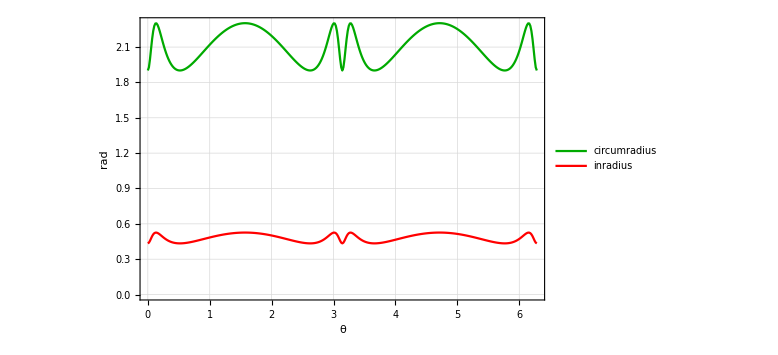

```mathematica
ListLinePlot[Map[getRadii[2,2π,#]&,{radiusCircumcenter,radiusIncenter}],
AxesLabel->{"t","radius"},
PlotLegends->{"circumradius","inradius"},Frame->True,
ImageSize->Large,FrameStyle->Large,
FrameLabel->{"θ","rad"},GridLines->Automatic,PlotStyle->Evaluate[(#/.ptClrs)&/@{"inc","cir"}]]
```

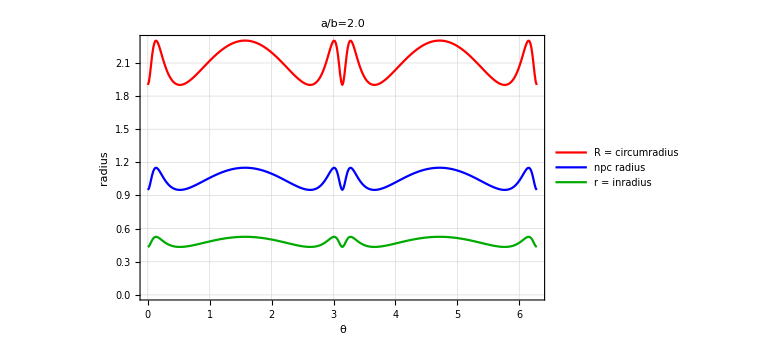

```mathematica
Module[{lab,radii,a=2},
radii=Map[getRadii[a,2π,#]&,{radiusCircumcenter,radiusNPC,radiusIncenter}];
lab="a/b="<>nfn[a,1];
ListLinePlot[radii,
AxesLabel->{"t","radius"}
(*,
Epilog->{Point@inMax,Dotted,Line[{{0,inMax[[1,2]]},{2π,inMax[[1,2]]}}]}*),
PlotLegends->Placed[Style[#,20]&/@{"R = circumradius","npc radius","r = inradius"},Right],
Frame->True,ImageSize->Large,FrameStyle->Large,GridLines->Automatic,
PlotRange->Automatic,
FrameLabel->{"θ","radius"},
PlotStyle->({#,Thick}&/@{Red,Blue,Darker@Green}),
PlotLabel->Style[lab,{Black,Large}]]]
```

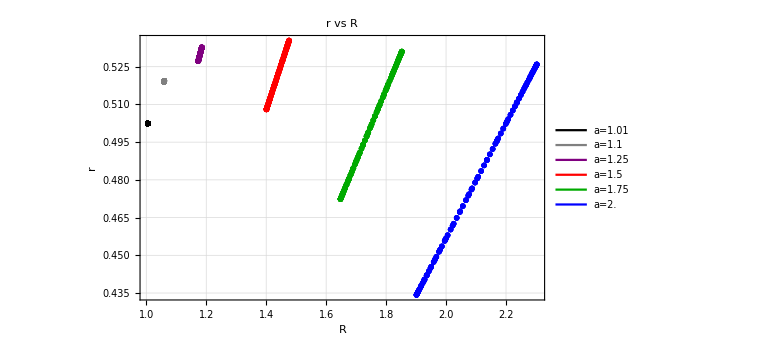

```mathematica
Module[{lab,cirRads,incRads,as={1.01,1.1,1.25,1.5,1.75,2.},clrs={Black,Gray,Purple,Red,Darker@Green,Blue}},
incRads=(Second/@getRadii[#,2π,radiusIncenter])&/@as;
cirRads=(Second/@getRadii[#,2π,radiusCircumcenter])&/@as;
lab="r vs R";
Legended[ListPlot[MapThread[Transpose@{#1,#2}&,{cirRads,incRads}],
PlotStyle->clrs,
Frame->True,ImageSize->Large,FrameStyle->Large,GridLines->Automatic,
PlotRange->All,
FrameLabel->{"R","r"},
PlotLabel->Style[lab,{Black,Large}]],LineLegend[clrs,Style[("a="<>ToString@#),16]&/@as]]]
```

```mathematica
Clear@getInRadCircumRadRatio;
getInRadCircumRadRatio[a_,t_]:=Module[{orbit,normals,r,R},
{orbit,normals}=orbitNormals[a,t];
r=radiusIncenter[orbit,normals][[2]];
R=radiusCircumcenter[orbit,normals][[2]];
{r,R,r/R}];
```

```mathematica
Clear@a
```

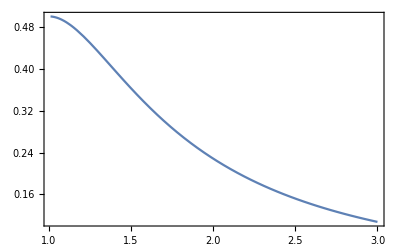

```mathematica
Plot[getInRadCircumRadRatio[a,0][[3]],{a,1.01,3},Frame->True]
```

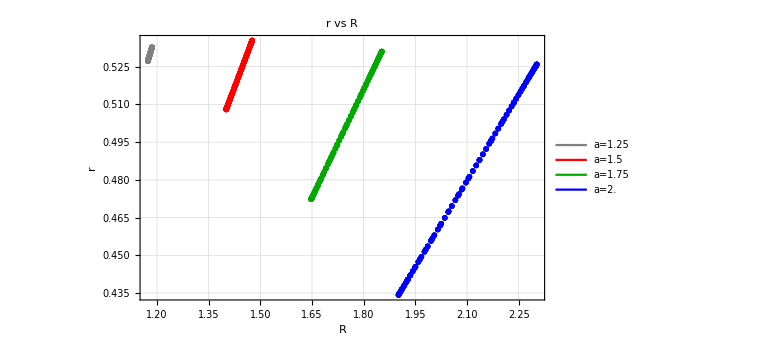

```mathematica
Module[{lab,cirRads,incRads,as={1.25,1.5,1.75,2.},clrs={Gray,Red,Darker@Green,Blue}},
incRads=(Second/@getRadii[#,2π,radiusIncenter])&/@as;
cirRads=(Second/@getRadii[#,2π,radiusCircumcenter])&/@as;
lab="r vs R";
Legended[ListPlot[MapThread[Transpose@{#1,#2}&,{cirRads,incRads}],
PlotStyle->clrs,
Frame->True,ImageSize->Large,FrameStyle->Large,GridLines->Automatic,
PlotRange->All,
FrameLabel->{"R","r"},
PlotLabel->Style[lab,{Black,Large}]],LineLegend[clrs,Style[("a="<>ToString@#),16]&/@as]]]
```

#### * Area of Triangle A=inradius*semiperimeter=r*s * Circumradius (R) is related to inradius (r) as follows: -Graphics-

```mathematica
getOrbitCosines[2,0]
```

{0.965424,0.131483,0.131483}

```mathematica
getOrbitCosineSum[a_,t_]:=Total[getOrbitCosines[a,t]];
```

```mathematica
getOrbitCosineSum[1.01,π]-1
```

0.499889

```mathematica
getOrbitCosineSum[1.5,π]-1
```

0.36266

```mathematica
getOrbitCosineSum[2,π]-1
```

0.22839

#### Cos[A] + Cos[B] + Cos[C] - 1 is constant!

```mathematica
Table[getOrbitCosineSum[1.5,t]-1,{t,0,2.π,π/100}]//Mean
```

0.36266

```mathematica
Table[getOrbitCosineSum[2,t]-1,{t,0,2.π,π/100}]//Mean
```

0.22839

```mathematica
Table[getOrbitCosineSum[2,t]-1,{t,0,2.π,π/100}]//StandardDeviation//Chop
```

0

#### Does the extriangle have a similar property, e.g., sum of sines is constant? Algebraically, no

#### Constraint on side lengths if sum of cosines is constant

```mathematica
Together[lawOfCosines[a,b,c]+lawOfCosines[b,c,a]+lawOfCosines[c,a,b]]
```

-(0.5 (1. a^3-1. a^2 b-1. a b^2+1. b^3-1. a^2 c-1. b^2 c-1. a c^2-1. b c^2+1. c^3))/(a b c)

Adding perimeter constancy doens' t help

```mathematica
(Together[lawOfCosines[a,b,c]+lawOfCosines[b,c,a]+lawOfCosines[c,a,b]]/.{c->P-a-b})//FullSimplify
```

(0.+2. b^2 P-2. b P^2+0.5 P^3+a^2 (-3. b+2. P)+a (-3. b^2+5. b P-2. P^2))/(a b (a+b-1. P))

An expression for P the perimeter

```mathematica
darbouxP[a]
```

(2 (1+a^2+√(1-a^2+a^4)) √(-1-a^2+2 √(1-a^2+a^4)))/(-1+a^2)

```mathematica
getTriPerimeters[a_,t_]:=Module[{orbit,normals,darboux,per},
{orbit,normals}=orbitNormals[a,t];
darboux=darbouxP[a];
per=Total[magn/@(orbit-RotateLeft[orbit])];
{per,darboux}]
```

```mathematica
getTriPerimeters[1.2,0]
```

{5.76226,5.76226}

```mathematica
(*FullSimplify[(
lawOfCosines[s1,s2,s3]+
lawOfCosines[s2,s3,s1]+
lawOfCosines[s3,s1,s2])/.
{s3->((darbouxP[a]/.Sqrt[1-a^2+a^4]->d)-s2-s1)},
a>0&d>0&s1>0&s2>0]*)
```

Identity: Cos[t]^2 = (cos[2 t] + 1)/2 => Cos[2t] = 2Cos[t]^2-1

```mathematica
cosAlpha[a,x1]^2
```

(a^4 (-1-a^2+2 √(1-a^2+a^4)))/((-1+a^2)^2 (a^4-(-1+a^2) x1^2))

#### Which means :

r/R = cos[A] + cos[B]+ cos[C]- 1

```mathematica
ratioInradiusCircumRadius[a_,t_]:=Module[{orbit,normals,R,r},
{orbit,normals}=orbitNormals[a,t];
R=radiusCircumcenter[orbit,normals][[2]];
r=radiusIncenter[orbit,normals][[2]];
r/R];
```

#### Prova cosA+cosB+cosC=1+r/R=constante Prof. Ronaldo Garcia

Correção 2 a expressão r/R :

```mathematica
getDelta[a_,b_:1]:=Module[{a2,b2},
a2=a^2;
b2=b^2;
Sqrt[a2^2-a2 b2+b2^2]
];
getOrbitCosineSumRG[a_,b_:1]:=Module[{a2,b2,a2plusb2,delta},
a2=a^2;
b2=b^2;
a2plusb2=a2+b2;
delta=getDelta[a,b];
a2plusb2(2delta-a2plusb2)/(a2-b2)^2];
ratioInrad2CircumRadRG[a_,b_:1]:=Module[{a2,b2,delta},
a2=a^2;
b2=b^2;
delta=getDelta[a,b];
2(delta-b2)(a2-delta)/(a2-b2)^2];
```

```mathematica
ratioInrad2CircumRadRG0[a_,b_:1]:=Module[{a2,b2,delta},
a2=a^2;
b2=b^2;
delta=getDelta[a,b];
2b2(delta-b2)/((a2-b2)(a2+delta))];
```

```mathematica
getOrbitCosineSumRG[2.]
```

1.22839

```mathematica
ratioInrad2CircumRadRG[2.]
```

0.22839

```mathematica
ratioInrad2CircumRadRG0[2.]
```

0.22839

### Plota razao constance : r/R = cosA + cosB + cosC - 1

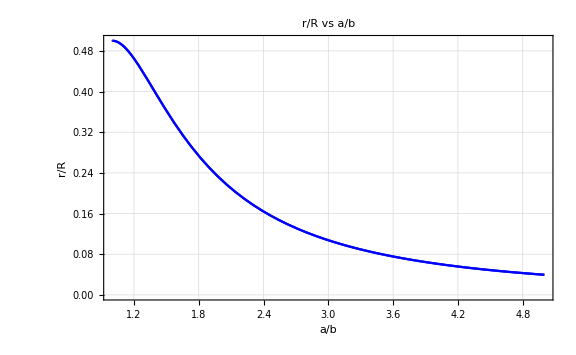

```mathematica
Plot[{
getOrbitCosineSum[a,0]-1,
getOrbitCosineSumRG[a]-1,
ratioInrad2CircumRadRG[a],
ratioInradiusCircumRadius[a,0]},{a,1,5},
Frame->True,FrameStyle->20
,ImageSize->Large,GridLines->Automatic,PlotStyle->{Thick,Blue},
FrameLabel->{"a/b","r/R"},PlotLabel->Style["r/R vs a/b",{Black,Large}]]
```

```mathematica
Plot3D[ratioInrad2CircumRadRG[a,b],{a,1,3},{b,1,3}]//Quiet
```

-Graphics3D-

```mathematica
getIncNpcDist[a_,t_]:=Module[{orbit,normals,inc,npc,feu},
{orbit,normals}=orbitNormals[a,t];
inc=radiusIncenter[orbit,normals];
npc=radiusNPC[orbit,normals];
feu=getFeuerbachpoint[npc[[1]],inc[[1]],inc[[2]]];
magn[inc[[1]]-feu]
];
getFeuNpcDist[a_,t_]:=Module[{orbit,normals,inc,npc,feu},
{orbit,normals}=orbitNormals[a,t];
inc=radiusIncenter[orbit,normals];
npc=radiusNPC[orbit,normals];
feu=getFeuerbachpoint[npc[[1]],inc[[1]],inc[[2]]];
magn[npc[[1]]-feu]
]
```

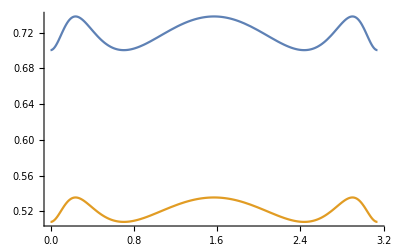

```mathematica
Plot[{getFeuNpcDist[1.5,t],
getIncNpcDist[1.5,t]},{t,0,π}]
```

## Numerically Calculate Exit Angle: α

```mathematica
Clear@gradDescPentErr;gradDescPentErr[a_,p1_,alpha0_,debug_:False]:=Module[{grad,dalpha=.0001,alpha,alphaSav,error=1,maxError=10^-6,eps=.001,it,itMax=1000,pentErr=1},
alpha=alpha0;
it=1;
While[error>maxError&&it<itMax,
it++;
pentErr=pentErrorP[a,p1,alpha];
grad=(pentErrorP[a,p1,alpha+dalpha]-pentErr)/dalpha;
alphaSav=alpha;
alpha=alpha-eps grad;
error=Abs[alpha-alphaSav];
If[debug&&Mod[it,100]==0,Print["it=",it,", error=",error]];
];
{it,error,alpha,pentErr}];
```

```mathematica
Clear@getPolyAlphaTOneQuarter;
getPolyAlphaTOneQuarter[errFn_,a_,alpha0_,degStep_:10,verbose_]:=Module[{lastAlpha,tRad,min,tab,ts,alphas,p1},
lastAlpha=alpha0;
tab=Table[
tRad=toRad[tDeg];
p1={a Cos[tRad],Sin[tRad]};
min=Quiet@FindMinimum[errFn[a,p1,alpha],{alpha,lastAlpha},
Method->"PrincipalAxis"(*,WorkingPrecision->40*)];
lastAlpha=(alpha/.min[[2]]);
(*min=gradDescPentErr[a,p1,lastAlpha];*)
(*lastAlpha=min[[3]];*)
If[verbose,Print["t=",tDeg,"; min=",min]];
{tDeg,tRad,lastAlpha,min},
(* takes advantage of 4-arc symmetry *)
{tDeg,0,90,degStep}];
{
"a"->a,
"tsDeg"->First/@tab,
"tsRad"->Second/@tab,
"alphas"->Third/@tab,
"mins"->(#[[4]]&/@tab)
}];
```

#### Takes Advantage of 4-arc alpha symmetry (only computes fn from 0 to 90)

```mathematica
Clear@doubleList;doubleList[vs_]:=Join[vs,Rest[Reverse@vs]];
Clear@quadrupleList;quadrupleList[vs_]:=Most[doubleList@doubleList@vs];
```

```mathematica
Clear@quadrupleT;
quadrupleT[theT_]:=Module[{degStep,radStep},
degStep=("tsDeg"/.theT)[[2]]-("tsDeg"/.theT)[[1]];
radStep=("tsRad"/.theT)[[2]]-("tsRad"/.theT)[[1]];
{
"a"->("a"/.theT),
"tsDeg"->Range[0,360-degStep,degStep],
"tsRad"->Range[0,2π-radStep,radStep],
"alphas"->quadrupleList["alphas"/.theT],
"mins"->quadrupleList["mins"/.theT]
}];
```

```mathematica
Clear@getPolyAlphaT;
getPolyAlphaT[errFn_,a_,startAlpha_,degStep_,verbose_]:=Module[{theT},
(* if the step angle is too large, the previous guess won't help *)
theT=getPolyAlphaTOneQuarter[errFn,a,startAlpha,degStep,verbose];
theT=quadrupleT@theT;
theT];
```

```mathematica
Clear@calcAlphaT;
calcAlphaT[doCalc_(*False for load*),errFn_,fname_,a_,startAlpha_,degStep_,verbose_:True]:=Module[{theT},
If[doCalc,
(* if the step angle is too large, the previous guess won't help *)
theT=getPolyAlphaT[errFn,a,startAlpha,degStep,verbose];
Print["saving: ",Length["alphas"/.theT]," records to",fname];
Save[fname,theT];
theT,
theT=Get[fname];
Print["loaded: ",Length["alphas"/.theT]," records from",fname];
theT]];
```

## Draw Poly

```mathematica
Clear@drawPoly;
Options[drawPoly]={drNotables->False,drSubtri->False,drLoci->False,drMedians->False,drExcentral->False,drCentroids->False,drCentroidLabels->False,drError->False,drCircs->False,drIncs->False,vtx->{1,2,3},plotAll->False};
drawPoly[polyErr_,notableLoci_,OptionsPattern[]]:=Module[{poly,a,centroids,centroidNames,lab,pnames,meds,polyTangs,polyInters,polyInterNames,tri1,notables,circs,incs,
lgt=.25,fnt=14},
poly="poly"/.polyErr;
a="a"/.polyErr;
centroids=getCentroids[poly];
centroidNames={"G_vtx","G_per","G_lam"};
lab="error: "<>nfn[N@("error"/.polyErr),3];
pnames=Take[{"A","B","C","D","E","F","G","H","I","J","K"},Length@poly];
meds=getMediansV@poly;
polyTangs=perp[ellGrad[a,#[[1]],#[[2]]]]&/@poly;
polyInters=MapThread[interRays[#1,#2,#3,#4]&,{poly,polyTangs,RotateLeft@poly,RotateLeft@polyTangs}];
polyInterNames=If[OptionValue@drExcentral,MapThread[(#1<>"'"<>#2<>"'")&,{pnames,RotateLeft@pnames}],{}];
(* *** *)
If[OptionValue@drCircs,Module[{sides,tri,cir},
circs=Table[
tri=Take[RotateLeft[poly,i-1],3];
cir=getCircumcenterTrilin[tri,RotateLeft@triLengths@tri];
(*cir=getCircumcenter@@tri;*)
{cir,magn[cir-tri[[1]]]},(* returns circumcenter and circumradius *)
{i,Length@poly}];
(*circs=Take[circs,1];*)
]];
If[OptionValue@drIncs,Module[{sides,tri,inc},
incs=Table[
tri=Take[RotateLeft[poly,i-1],3];
inc=getIncenterTrilin[tri,RotateLeft@triLengths@tri];
(*cir=getCircumcenter@@tri;*)
{inc,closestDist[inc,tri[[1]],tri[[2]]]},(* returns circumcenter and circumradius *)
{i,Length@poly}];
(*circs=Take[circs,1];*)
]];
If[OptionValue@drNotables||OptionValue@drSubtri,Module[{normals},
tri1=Part[poly,OptionValue@vtx];
normals=getTriBisectors@@tri1;
notables=getNotables[tri1,normals];
]];
gr=Graphics[{PointSize@Large,Point@poly,FaceForm@None,
{EdgeForm[{Black,Thick}],FaceForm@Gray,Opacity@.1,Polygon@poly,Black,Point@poly},
{Black,Arrowheads[Medium],MapThread[drawArrow[#1,norm[perpNeg[#2]],lgt]&,{poly,polyTangs}]},
If[OptionValue@drCentroids,{Black,MapThread[{Point@#1,If[OptionValue@drCentroidLabels,Text[Style[#2,14],#1,{0,-1.5}],{}]}&,{centroids,centroidNames}]},{}],
If[OptionValue@drExcentral,{EdgeForm@Darker@Green,Polygon@polyInters,Darker@Green,Point@polyInters,
MapThread[Text[Style[#1,fnt],#2,{-1.25,-1.25}]&,{polyInterNames,polyInters}]},{}],
{Black,MapThread[Text[Style[#1,fnt],ray[#2,norm[perp[#3]],lgt/2]]&,{pnames,poly,polyTangs}]},
If[OptionValue@drMedians,{{Dashed,Blue,Line[{#,{0,0}}]&/@polyInters},
{Blue,Point@meds,Point@{0,0}}},{}],
If[OptionValue@drCircs,{Red,{Dashed,Circle[#[[1]],#[[2]]]&/@circs},Point[First/@circs],Circle[circs[[1,1]],.05]},{}
],
If[OptionValue@drIncs,{Darker@Green,Dashed,Circle[#[[1]],#[[2]]]&/@incs,Point[First/@incs]},{}
],
If[OptionValue@drNotables,{List@@drawSomeNotables[notables,First@notableLoci],EdgeForm@None,FaceForm@Red,Opacity@.1,Polygon@tri1},{}],
If[OptionValue@drSubtri,{EdgeForm@None,FaceForm@Red,Opacity@.2,Polygon@tri1},{}]
}];
Show[{plotEll[a],gr,If[OptionValue@drLoci,Second@notableLoci,{}]},
If[OptionValue@drError,PlotLabel->lab,{}],
PlotRange->(If[OptionValue@plotAll,All,{{-2,2},{-1,1}}]),
Frame->True,FrameStyle->Medium,
AxesStyle->Directive[{Dotted,Gray}]]];
```

```mathematica
Clear@showOnePoly;
showOnePoly[alphaT_,i_,notableLoci_,fnVtx0_,fnErrorP_,opts:OptionsPattern[]]:=Module[{polyErr},
polyErr=polyError[alphaT,i,fnVtx0,fnErrorP];
drawPoly[polyErr,notableLoci,FilterRules[{opts}, Options[drawPoly]]]];
```

```mathematica
Clear@getPolyNotableLoci;
getPolyNotableLoci[alphaT_,fnVtx0_,vtx_:{1,2,3},nots_:{"inc","bar","ort"}]:=Module[{polys,normals,tris,notables},
(*{"cir","npc","mit","feu"};*)
polys=Table[polyVtx[alphaT,i,fnVtx0],{i,Length["alphas"/.alphaT]}];
polys=Append[polys,First@polys];
tris=Part[#,vtx]&/@polys;
normals=getTriBisectors@@#&/@tris;
notables=MapThread[getNotables[#1,#2]&,{tris,normals}];
{nots,ListLinePlot[Transpose[nots/.notables],PlotStyle->(nots/.ptClrs)]}
];
```

```mathematica
makeVtxLabs[vtxList_]:=StringJoin/@Map[ToString,vtxList,{2}];
```

```mathematica
Clear@manipulatePolyVtx;
manipulatePolyVtx[alphaT_,notableLociList_,fnVtx0_,fnErrorP_,vtxList_:{{1,2,3}}]:=Module[{vtxLabs,vtxMatch,lociMatch},
vtxLabs=makeVtxLabs@vtxList;
Manipulate[
vtxMatch=First@FirstPosition[vtxLabs,tri];
lociMatch=notableLociList[[vtxMatch]];
Show[
showOnePoly[alphaT,i,
lociMatch,fnVtx0,fnErrorP,
drNotables->drNotables0,drSubtri->drSubtri0,drLoci->drLoci0,
drExcentral->drExcentral0,drCentroids->drCentroids0,drCentroidLabels->drCentroidLabels0,drCircs->drCircs0,
drIncs->drIncs0,plotAll->plotAll0,
vtx->vtxList[[vtxMatch]]],ImageSize->Large],
{{i,1},1,Length["alphas"/.alphaT],1,Appearance->"Labeled"},
{{drExcentral0,False,"excentral"},{True,False}},
{{drSubtri0,False,"subtri"},{True,False}},
{{drNotables0,True,"notables"},{True,False}},
{{drLoci0,True,"loci"},{True,False}},
{{drCentroids0,True,"centroids"},{True,False}},
{{drCentroidLabels0,False,"centroidLabels"},{True,False}},
{{drCircs0,False,"circs"},{True,False}},
{{drIncs0,False,"incs"},{True,False}},
{{tri,vtxLabs[[1]]},vtxLabs},
{{plotAll0,False,"plotAll"},{True,False}},SaveDefinitions->True]];
```

```mathematica
Clear@showOneLocusVtx;
Options[showOneLocusVtx]={filling->None,fillingStyle->{Opacity@.1},plotAll->False};
showOneLocusVtx[a_,i_,lociList_,vtxList_,vtx_,OptionsPattern[]]:=Module[{vtxLabs},
vtxLabs=makeVtxLabs@vtxList;
Show[{plotEll[a],
ListLinePlot[
MapIndexed[If[vtx=="all"||vtx==#1,Legended[lociList[[First@#2,i]],vtxLabs[[First@#2]]],{{0,0}}]&,vtxLabs],
Filling->(OptionValue@filling),FillingStyle->(OptionValue@fillingStyle),PlotStyle->Thick
(*PlotStyle->{Blue,Red,Darker@Green}*)]},Frame->True,FrameStyle->Medium,PlotRange->(If[OptionValue@plotAll,All,{{-2,2},{1,1}}]),
PlotLabel->Style[centerNames[[i]]<>", a/b="<>nfn[a,2],{Black,16}],ImageSize->Large]];
```

```mathematica
Clear@manipulateLociVtx;
manipulateLociVtx[alphaT_,lociList_,vtxList_:{{1,2,3}},opts:OptionsPattern[]]:=Module[{a,vtxLabs},
a="a"/.alphaT;
vtxLabs=makeVtxLabs@vtxList;
Manipulate[showOneLocusVtx[a,i,lociList,vtxList,vtx,FilterRules[{opts,plotAll->plotAll0}, Options[showOneLocusVtx]]],
{{i,1},1,Length[centerNames],1,Appearance->"Labeled"},
{{vtx,"all"},{"all",Sequence@@vtxLabs}},
{{plotAll0,True,"plotAll"},{True,False}},SaveDefinitions->True]];
```

```mathematica
makeOneLociRow[alphaT_,lociList_,vtxList_,i_,showAll_:True,opts:OptionsPattern[]]:=Module[{a,vtxLabs},
vtxLabs=makeVtxLabs@vtxList;
a="a"/.alphaT;
Grid[{showOneLocusVtx[a,i,lociList,vtxList,#,FilterRules[{opts}, Options[showOneLocusVtx]]]&/@If[showAll,Prepend[vtxLabs,"all"],vtxLabs]}]];
```

#### Poly Vert

```mathematica
Clear@rotPoly;
rotPoly[a_,poly_]:=Module[{tangs,bis,mtx,polyRot,bisRot},
tangs=perp[ellGrad[a,#[[1]],#[[2]]]]&/@poly;
bis=norm[perpNeg[#]]&/@tangs;
mtx={perp@bis[[1]],-bis[[1]]};
polyRot=(mtx.#+{0,1})&/@((#-poly[[1]])&/@poly);
bisRot=(mtx.#)&/@bis;
{polyRot,bis,bisRot}
];
```

```mathematica
Clear@drawPolyVert;
drawPolyVert[polyErr_,drBack_:True]:=Module[{a,poly,centroid,lab,pnames,polyRot,polyBisectors,polyBisectorsRot,centroidRot,
lgt=.33,fnt=14},
a="a"/.polyErr;
poly="poly"/.polyErr;
centroid=RegionCentroid@Polygon@poly;
lab="error: "<>nfn[N@("error"/.polyErr),3];
pnames=Take[{"A","B","C","D","E","F","G","H","I","J","K"},Length@poly];
{polyRot,polyBisectors,polyBisectorsRot}=rotPoly[a,poly];
centroidRot=RegionCentroid@Polygon@polyRot;
(*polyInters=MapThread[interRays[#1,#2,#3,#4]&,{poly,polyTangs,RotateLeft@poly,RotateLeft@polyTangs}];
polyInterNames={"p12","p23","p34","p45","p51"};*)
gr=Graphics[{PointSize@Large,FaceForm@None,Arrowheads[Medium],
{EdgeForm[{Red,Thick}],FaceForm@Gray,Opacity@.3,Polygon@polyRot},
{Black,Point@polyRot,Black,drawArrow[{0,1},{0,-1},1.5*lgt],"bar"/.ptClrs,Point@centroidRot,Text[Style["G'",14],centroidRot,{0,-1.5}]},
MapThread[Text[Style[#1<>"'",{Lighter@Red,fnt}],ray[#2,-#3,lgt/2]]&,{pnames,polyRot,polyBisectorsRot}],
If[drBack,
{{EdgeForm[{Gray,Dashed}],Polygon@poly,Gray,Point@poly,Point@centroid,Text[Style["G",14],centroid,{0,-1.5}]},
{Lighter@Gray,MapThread[drawArrow[#1,#2,lgt]&,{poly,polyBisectors}]},
MapThread[Text[Style[#1,{Lighter@Gray,fnt}],ray[#2,-#3,lgt/2]]&,{pnames,poly,polyBisectors}]},{}]
}];
Show[{plotEll[a,Lighter@Gray],gr},AxesStyle->Directive[Lighter@Gray],Frame->True,PlotRange->{{-2,2},{-1.2,1.2}}]];
```

```mathematica
Clear@getPolyVertLoci;
getPolyVertLoci[alphaT_,fnVtx0_] := Module[{a,polys,centroids, polyRots, centroidsRot,toPlot},
a="a"/.alphaT;
polys=Table[polyVtx[alphaT,i,fnVtx0],{i,Length["alphas"/.alphaT]}];
centroids = RegionCentroid[Polygon[#]] & /@ polys;
polyRots=First/@(rotPoly[a,#]&/@polys);
(*polyRots = rotpoly[a, #] & /@ polys;*)
centroidsRot = RegionCentroid[Polygon[#]] & /@ polyRots;
(*toPlot={Second /@ polyRots, Third /@ polyRots, Fourth /@ polyRots, Fifth /@ polyRots};*)
toPlot=Rest@Transpose[polyRots];
ListLinePlot[{Sequence@@toPlot, centroids,centroidsRot}, Axes -> False]
   ];
```

```mathematica
Clear@showOnePolyVert;
showOnePolyVert[alphaT_, i_, polyVertLoci_,fnVtx0_,fnErrorP_, drBack_: True] := 
Module[{a, p1, t, alpha,polyErr},
polyErr=polyError[alphaT,i,fnVtx0,fnErrorP];
Show[{drawPolyVert[polyErr, drBack], polyVertLoci},
PlotRange -> {{-2, 2}, {-2, 2}},
Frame -> True, FrameStyle -> Medium,
AxesStyle -> Directive[{Dotted, Gray}]]];
```

## Triangle (Simulate AlphaT)

```mathematica
Clear@getEllVtx0;(* not for error purposes *)
getEllVtx0[a_,p1_,alpha_]:={p1};
triErrorP[a_,p1_,alpha_]:=0;
```

```mathematica
getEllAlphaT[a_]:=Module[{tsDeg,tsRad,alphas},
tsDeg=Range[360]-1;
tsRad=toRad/@tsDeg;
alphas=ConstantArray[0,Length@tsRad];
{"a"->a,"tsDeg"->tsDeg,
"tsRad"->tsRad,
"alphas"->alphas}];
```

```mathematica
ellAlphaT15=getEllAlphaT[1.5];
(*Save["data/ellAlphaT_a15.m",ellAlphaT15];*)
```

```mathematica
getTriAlphaT[a_]:=Module[{tsDeg,tsRad,alphas},
tsDeg=Range[360]-1;
tsRad=toRad/@tsDeg;
alphas=getAlpha[a,#]&/@tsRad;
{"a"->a,"tsDeg"->tsDeg,
"tsRad"->tsRad,
"alphas"->alphas}];
```

```mathematica
triAlphaT15=getTriAlphaT[1.5];
(*Save["data/triAlphaT_a15.m",triAlphaT15];*)
```

```mathematica
Clear@getTriVtx0;(* not for error purposes *)
getTriVtx0[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
{p1,p2,p2Neg}];
```

```mathematica
triLociTable15=getLociTablePoly[triAlphaT15,getTriVtx0,{1,2,3}];
triLociTable15//Dimensions
```

{100,361,2}

```mathematica
manipulateLociVtx[triAlphaT15,{triLociTable15}]
```

## Quadrangle

```mathematica
Clear@getQuadVtx;
getQuadVtx[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3,p3Neg},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
p3=getInterRefl[a,p1,p2];
p3Neg=getInterRefl[a,p1,p2Neg];
{p2,p2Neg,p3,p3Neg}];
Clear@getQuadVtx0;(* not for error purposes *)
getQuadVtx0[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
p3=getInterRefl[a,p1,p2];
{p1,p2,p3,p2Neg}];
```

```mathematica
Clear@quadError;
quadError[a_,t_,alpha_]:=Module[{p1,qv},
p1={a Cos[t],Sin[t]};
qv=getQuadVtx[a,p1,alpha];
(* p3Neg - p3 *)
magn2[qv[[3]]-qv[[4]]]];
quadErrorP[a_,p1_,alpha_]:=Module[{qv},
qv=getQuadVtx[a,p1,alpha];
(* p3Neg - p3 *)
magn2[qv[[3]]-qv[[4]]]];
```

```mathematica
doQuadAlphaT15=True;Clear@quadAlphaT15;
quadAlphaT15=calcAlphaT[doQuadAlphaT15,quadErrorP,"data/quadAlphaT_a15.m",1.5,.794,1,False];
```

saving: 360 records todata/quadAlphaT_a15.m

#### Loci Table

```mathematica
quadLociTable15=getLociTablePoly[quadAlphaT15,getQuadVtx0,{1,2,3}];
quadLociTable15//Dimensions
```

{100,361,2}

```mathematica
manipulateLociVtx[quadAlphaT15,{quadLociTable15}]
```

## Pentagon

```mathematica
Clear@getPentVtx;
getPentVtx[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3,p3Neg,p4,p4Neg},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
p3=getInterRefl[a,p1,p2];
p4=getInterRefl[a,p2,p3];
p3Neg=getInterRefl[a,p1,p2Neg];
p4Neg=getInterRefl[a,p2Neg,p3Neg];
{p2,p2Neg,p3,p3Neg,p4,p4Neg}];

Clear@getPentVtx0;(* not for error purposes *)
getPentVtx0[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3,p3Neg},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
p3=getInterRefl[a,p1,p2];
p3Neg=getInterRefl[a,p1,p2Neg];
{p1,p2,p3,p3Neg,p2Neg}];
```

```mathematica
Clear@pentErrorP;pentErrorP[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3,p3Neg,p4,p4Neg},
{p2,p2Neg,p3,p3Neg,p4,p4Neg}=getPentVtx[a,p1,alpha];
(* p3Neg - p3 *)
magn2[p3Neg-p4]+magn2[p3-p4Neg]];
Clear@pentErrorPabs;pentErrorPabs[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3,p3Neg,p4,p4Neg},
{p2,p2Neg,p3,p3Neg,p4,p4Neg}=getPentVtx[a,p1,alpha];
(* p3Neg - p3 *)
magn[p3Neg-p4]+magn[p3-p4Neg]];
```

```mathematica
Clear@pentError;
pentError[a_,t_,alpha_]:=Module[{p1,pv},
p1={a Cos[t],Sin[t]};
pentErrorP[a,p1,alpha]];
```

#### Pentagon Exit Angle Table

```mathematica
doPentAlphaT125=False;Clear@pentAlphaT125;
pentAlphaT125=calcAlphaT[doPentAlphaT125,pentErrorPabs,"data/pentAlphaT_a125.m",1.25,.86,10,False];
```

loaded: 36 records fromdata/pentAlphaT_a125.m

```mathematica
doPentAlphaT15=False;Clear@pentAlphaT15;
pentAlphaT15=calcAlphaT[doPentAlphaT15,pentErrorPabs,"data/pentAlphaT_a15.m",1.5,.794,1,True];
```

loaded: 360 records fromdata/pentAlphaT_a15.m

```mathematica
doPentAlphaT20=False;Clear@pentAlphaT20;
pentAlphaT20=calcAlphaT[doPentAlphaT20,pentErrorPabs,"data/pentAlphaT_a20.m",2.0,.69,10,False];
```

loaded: 36 records fromdata/pentAlphaT_a20.m

```mathematica
doPentAlphaT30=False;Clear@pentAlphaT30;
pentAlphaT30=calcAlphaT[doPentAlphaT30,pentErrorPabs,"data/pentAlphaT_a30.m",3.0,.55,5,False];
```

loaded: 72 records fromdata/pentAlphaT_a30.m

```mathematica
reportErrorsAlphaT[alphaT_]:=Module[{errors},
errors=First/@("mins"/.alphaT);
{Length@errors,Mean@errors,Max@errors,Min@errors}]
```

```mathematica
reportErrorsAlphaT/@{pentAlphaT125,pentAlphaT15,pentAlphaT20,pentAlphaT30}//ColumnForm
```

{36,3.13753×10^-13,1.41451×10^-12,7.08896×10^-16}
{360,3.23944×10^-6,0.000291471,6.07529×10^-16}
{36,3.39754×10^-13,2.76421×10^-12,2.16162×10^-15}
{72,4.05773×10^-7,5.79672×10^-6,2.0542×10^-15}

#### Loci Table

```mathematica
pentLociTableList15=getLociTablePoly[pentAlphaT15,getPentVtx0,#]&/@pentVtxList;
Dimensions/@pentLociTableList15
```

pentVtxList

```mathematica
manipulateLociVtx[pentAlphaT15,pentLociTableList15,pentVtxList]
```

## Hexagon

```mathematica
Clear@getHexVtx;
getHexVtx[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3,p3Neg,p4,p4Neg},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
p3=getInterRefl[a,p1,p2];
p4=getInterRefl[a,p2,p3];
p3Neg=getInterRefl[a,p1,p2Neg];
p4Neg=getInterRefl[a,p2Neg,p3Neg];
{p2,p2Neg,p3,p3Neg,p4,p4Neg}];

Clear@getHexVtx0;(* not for error purposes *)
getHexVtx0[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3,p4,p3Neg},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
p3=getInterRefl[a,p1,p2];
p4=getInterRefl[a,p2,p3];
p3Neg=getInterRefl[a,p1,p2Neg];
{p1,p2,p3,p4,p3Neg,p2Neg}];
```

```mathematica
Clear@hexErrorP;hexErrorP[a_,p1_,alpha_]:=Module[{p4,p4Neg},
{p4,p4Neg}=Part[getHexVtx[a,p1,alpha],{5,6}];
(* p3Neg - p3 *)
magn2[p4-p4Neg]];
Clear@hexErrorPabs;hexErrorPabs[a_,p1_,alpha_]:=Sqrt@hexErrorP[a,p1,alpha];
```

```mathematica
Clear@hexError;
hexError[a_,t_,alpha_]:=Module[{p1,pv},
p1={a Cos[t],Sin[t]};
hexErrorP[a,p1,alpha]];
```

#### Hexagon Exit Angle Table

```mathematica
doHexAlphaT15=False;Clear@hexAlphaT15;
hexAlphaT15=calcAlphaT[doHexAlphaT15,hexErrorPabs,"data/hexAlphaT_a15.m",1.5,.9273,1,True];
```

loaded: 360 records fromdata/hexAlphaT_a15.m

#### Loci Table

```mathematica
hexLociTableList15=getLociTablePoly[hexAlphaT15,getHexVtx0,#]&/@hexVtxList;
Dimensions/@hexLociTableList15
```

{{100,361,2},{100,361,2},{100,361,2}}

```mathematica
getMinCircularity/@hexLociTableList15
```

{{0.0147021,X(5): NINE-POINT CENTER},{0.129684,X(98): TARRY POINT},{0.00760781,X(10): SPIEKER CENTER}}

#### X(10) [Spieker] is near circular and X(99) [Steiner] is near billiard

```mathematica
manipulateLociVtx[hexAlphaT15,hexLociTableList15,hexVtxList]
```

## Heptagon

```mathematica
Clear@getHeptVtx;
getHeptVtx[a_,p1_,alpha_]:=Module[{p2,p2Neg,p3,p3Neg,p4,p4Neg,p5,p5Neg},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
p3=getInterRefl[a,p1,p2];
p4=getInterRefl[a,p2,p3];
p5=getInterRefl[a,p3,p4];
p3Neg=getInterRefl[a,p1,p2Neg];
p4Neg=getInterRefl[a,p2Neg,p3Neg];
p5Neg=getInterRefl[a,p3Neg,p4Neg];
{p2,p2Neg,p3,p3Neg,p4,p4Neg,p5,p5Neg}];

Clear@getHeptVtx0;(* not for error purposes *)
getHeptVtx0[a_,p1_,alpha_]:=Module[{p2,p3,p4,p2Neg,p3Neg,p4Neg},
{p2,p2Neg}=getP2Alpha[a,p1,alpha];
p3=getInterRefl[a,p1,p2];
p4=getInterRefl[a,p2,p3];
p3Neg=getInterRefl[a,p1,p2Neg];
p4Neg=getInterRefl[a,p2Neg,p3Neg];
{p1,p2,p3,p4,p4Neg,p3Neg,p2Neg}];
```

```mathematica
Clear@heptErrorP;heptErrorP[a_,p1_,alpha_]:=Module[{p4,p4Neg,p5,p5Neg},
{p4,p4Neg,p5,p5Neg}=Part[getHeptVtx[a,p1,alpha],{5,6,7,8}];
magn2[p4-p5Neg]+magn2[p5-p4Neg]];
Clear@heptErrorPabs;heptErrorPabs[a_,p1_,alpha_]:=Sqrt@heptErrorP[a,p1,alpha];
```

```mathematica
Clear@heptError;
heptError[a_,t_,alpha_]:=Module[{p1,pv},
p1={a Cos[t],Sin[t]};
heptErrorP[a,p1,alpha]];
```

```mathematica
heptVtxList={{1,2,3},{1,2,4},{1,2,5},{1,3,5}};
```

#### Heptagon Exit Angle Table

```mathematica
doHeptAlphaT15=False;Clear@heptAlphaT15;
heptAlphaT15=calcAlphaT[doHeptAlphaT15,heptErrorP,"data/heptAlphaT_a15.m",1.5,1.02,1,True];
```

loaded: 360 records fromdata/heptAlphaT_a15.m

```mathematica
heptLociTableList15=getLociTablePoly[heptAlphaT15,getHeptVtx0,#]&/@heptVtxList;
Dimensions/@heptLociTableList15
```

{{100,361,2},{100,361,2},{100,361,2},{100,361,2}}

#### Loci

```mathematica
manipulateLociVtx[heptAlphaT15,heptLociTableList15,heptVtxList]
```

## Save Hept Loci to Disk

{123,124,125,135}

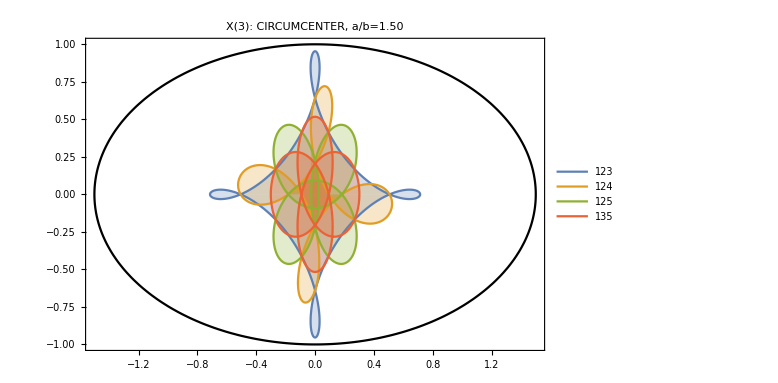
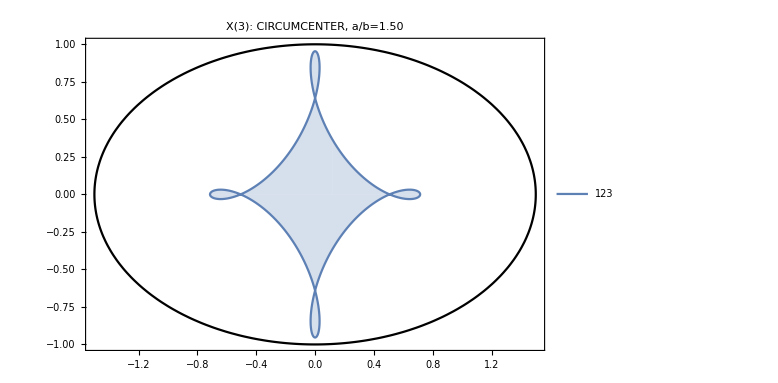
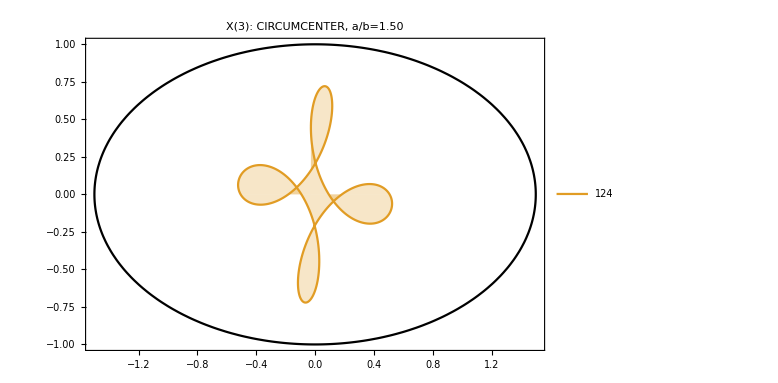
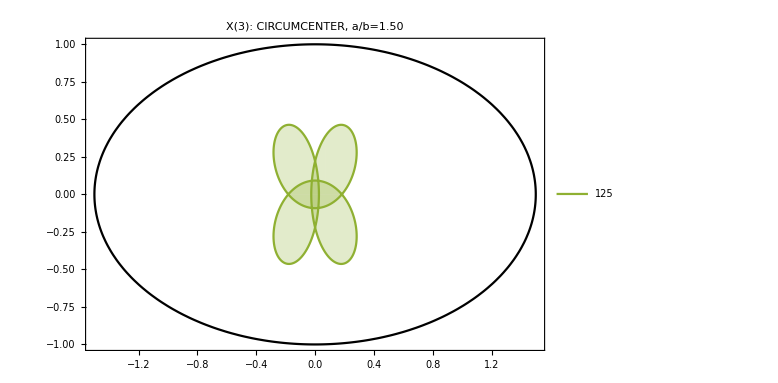
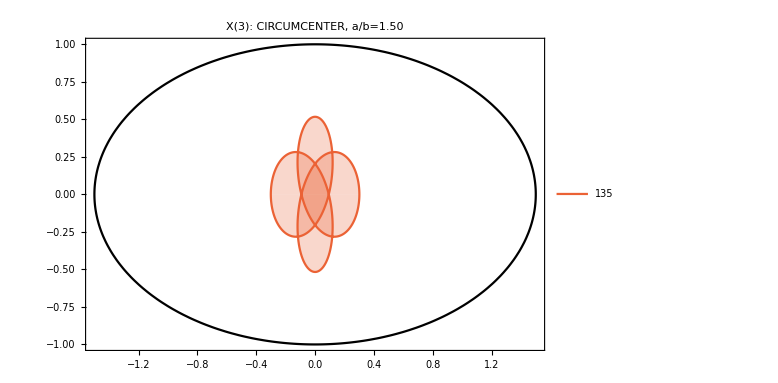
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
makeOneLociRow[heptAlphaT15,heptLociTableList15,heptVtxList,3,True,plotAll->True,filling->Axis,fillingStyle->Opacity@.25]
```

```mathematica
doExportLoci=False;
If[doExportLoci,
CreateDirectory/@{"loci_quad","loci_pent","loci_hex","loci_hept"};
Export["loci_quad/quadRow"<>padn[#]<>".png",makeOneLociRow[quadAlphaT15,{quadLociTable15},{{1,2,3}},#,False]]&/@Range[Length[centerNames]];
Export["loci_pent/pentRow"<>padn[#]<>".png",makeOneLociRow[pentAlphaT15,pentLociTableList15,pentVtxList,#]]&/@Range[Length[centerNames]];
Export["loci_hex/hexRow"<>padn[#]<>".png",makeOneLociRow[hexAlphaT15,hexLociTableList15,hexVtxList,#]]&/@Range[Length[centerNames]];
Export["loci_hept/heptRow"<>padn[#]<>".png",makeOneLociRow[heptAlphaT15,heptLociTableList15,heptVtxList,#]]&/@Range[Length[centerNames]];
];
```

```mathematica
doExportLociAll=True;
If[doExportLociAll,
CreateDirectory/@{"loci_quad_all","loci_pent_all","loci_hex_all","loci_hept_all"};
Export["loci_quad_all/quadRow"<>padn[#]<>".png",makeOneLociRow[quadAlphaT15,{quadLociTable15},{{1,2,3}},#,False,plotAll->True]]&/@Range[Length[centerNames]];
Export["loci_pent_all/pentRow"<>padn[#]<>".png",makeOneLociRow[pentAlphaT15,pentLociTableList15,pentVtxList,#,True,plotAll->True]]&/@Range[Length[centerNames]];
Export["loci_hex_all/hexRow"<>padn[#]<>".png",makeOneLociRow[hexAlphaT15,hexLociTableList15,hexVtxList,#,True,plotAll->True]]&/@Range[Length[centerNames]];
Export["loci_hept_all/heptRow"<>padn[#]<>".png",makeOneLociRow[heptAlphaT15,heptLociTableList15,heptVtxList,#,True,plotAll->True]]&/@Range[Length[centerNames]];
];
```

```mathematica
Clear@showOneSubTriRow;
showOneSubTriRow[alphaT_,fnVtx0_,vtxList_]:=Grid[{Show[
showOnePoly[alphaT,31,{},fnVtx0,Function[x,0],drSubtri->True,drCentroids->False,vtx->#],
ImageSize->400,PlotRange->{{-1.6,1.6},{-1,1}}]&/@vtxList}];
```

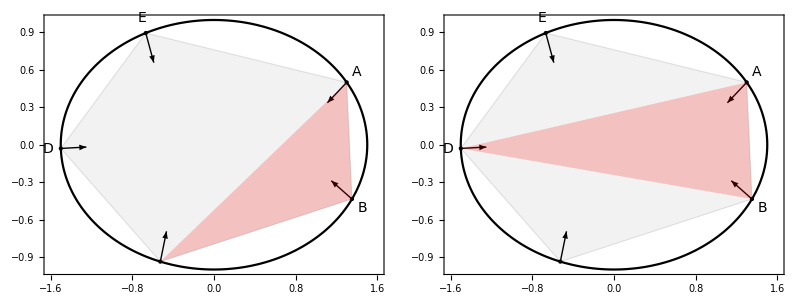

```mathematica
showOneSubTriRow[pentAlphaT15,getPentVtx0,pentVtxList]
```

```mathematica
subTriImgs=MapThread[showOneSubTriRow[#1,#2,#3]&,
{{quadAlphaT15,pentAlphaT15,hexAlphaT15,heptAlphaT15},
{getQuadVtx0,getPentVtx0,getHexVtx0,getHeptVtx0},
{{{1,2,3}},pentVtxList,hexVtxList,heptVtxList}}];
```

```mathematica
Show[Rasterize@Grid[Transpose@{subTriImgs},Alignment->Left],ImageSize->400]
```

-Graphics-

```mathematica
Length@subTriImgs
```

1

```mathematica
Export["subtris_N="<>ToString@#<>".png",subTriImgs[[#-3]]]&/@Range[4,7,1]
```

{subtris_N=4.png,subtris_N=5.png,subtris_N=6.png,subtris_N=7.png}